# My glucose series

## Program

```mathematica
getTimeSer[gs_]:=Module[{tr},
tr=Transpose[gs];
TimeSeries[tr[[2]],{tr[[1]]}]]
```

```mathematica
getMarkPos[ser_]:=Position[ser,{_,_,{_String}}]
```

```mathematica
getMarkedDate[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
Map[#[[1]]&,ser[[pos]]]
]
```

```mathematica
getMarkedItem[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
ser[[pos]]
]
```

```mathematica
timeShift=2209021200
```

2209021200

```mathematica
AbsoluteTime[]-UnixTime[]
```

2.209021200699592×10^9

```mathematica
(* createEpilog[gs_]:=Map[Text["*",{UnixTime[#]+timeShift,80}]&,getMarkedDate[gs]] *)
```

```mathematica
createEpilog[gs_]:=Map[Text[#[[3]],{UnixTime[#[[1]]]+timeShift,80}]&,getMarkedItem[gs]]
```

## Data

```mathematica
gs=Get["/Users/kouamano/Profile/blood-glc.txt"]
```

{{Thu 3 Feb 2022 06:05:00GMT+9,148,{}},{Thu 3 Feb 2022 11:16:00GMT+9,396,{}},{Thu 3 Feb 2022 16:31:00GMT+9,257,{}},{Fri 4 Feb 2022 06:06:00GMT+9,177,{}},{Fri 4 Feb 2022 11:16:00GMT+9,273,{}},{Fri 4 Feb 2022 18:30:00GMT+9,204,{}},{Sat 5 Feb 2022 05:57:00GMT+9,98,{}},{Sat 5 Feb 2022 12:15:00GMT+9,137,{}},{Sat 5 Feb 2022 17:15:00GMT+9,226,{}},{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Sun 6 Feb 2022 12:21:00GMT+9,374,{}},{Sun 6 Feb 2022 17:28:00GMT+9,241,{}},{Mon 7 Feb 2022 06:17:00GMT+9,158,{}},{Mon 7 Feb 2022 11:34:00GMT+9,293,{}},{Mon 7 Feb 2022 16:44:00GMT+9,382,{}},{Tue 8 Feb 2022 06:23:00GMT+9,152,{}},{Tue 8 Feb 2022 12:09:00GMT+9,399,{}},{Tue 8 Feb 2022 17:05:00GMT+9,275,{}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Wed 9 Feb 2022 11:54:00GMT+9,348,{}},{Wed 9 Feb 2022 17:04:00GMT+9,271,{}},{Thu 10 Feb 2022 06:21:00GMT+9,216,{}},{Thu 10 Feb 2022 11:54:00GMT+9,133,{}},{Thu 10 Feb 2022 17:01:00GMT+9,264,{}},{Fri 11 Feb 2022 06:25:00GMT+9,191,{}},{Fri 11 Feb 2022 12:00:00GMT+9,197,{}},{Fri 11 Feb 2022 17:04:00GMT+9,224,{}},{Sat 12 Feb 2022 06:23:00GMT+9,165,{}},{Sat 12 Feb 2022 12:09:00GMT+9,210,{}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}},{Sun 13 Feb 2022 06:17:00GMT+9,217,{}},{Sun 13 Feb 2022 12:27:00GMT+9,286,{}},{Sun 13 Feb 2022 17:23:00GMT+9,300,{}},{Mon 14 Feb 2022 06:12:00GMT+9,211,{}},{Mon 14 Feb 2022 12:18:00GMT+9,245,{}},{Mon 14 Feb 2022 18:49:00GMT+9,204,{}},{Tue 15 Feb 2022 06:18:00GMT+9,199,{}},{Tue 15 Feb 2022 11:59:00GMT+9,287,{}},{Tue 15 Feb 2022 18:21:00GMT+9,205,{}},{Wed 16 Feb 2022 06:15:00GMT+9,226,{}},{Wed 16 Feb 2022 12:16:00GMT+9,308,{}},{Wed 16 Feb 2022 18:27:00GMT+9,242,{}},{Thu 17 Feb 2022 06:21:00GMT+9,238,{}},{Thu 17 Feb 2022 12:07:00GMT+9,209,{}},{Thu 17 Feb 2022 19:06:00GMT+9,210,{}},{Fri 18 Feb 2022 06:11:00GMT+9,190,{}},{Fri 18 Feb 2022 12:12:00GMT+9,288,{}},{Fri 18 Feb 2022 19:21:00GMT+9,211,{}},{Sat 19 Feb 2022 06:13:00GMT+9,231,{}},{Sat 19 Feb 2022 12:17:00GMT+9,231,{}},{Sat 19 Feb 2022 17:55:00GMT+9,179,{}},{Sun 20 Feb 2022 06:52:00GMT+9,217,{}},{Sun 20 Feb 2022 12:20:00GMT+9,243,{}},{Sun 20 Feb 2022 17:42:00GMT+9,244,{}},{Mon 21 Feb 2022 06:20:00GMT+9,197,{}},{Mon 21 Feb 2022 12:07:00GMT+9,206,{}},{Mon 21 Feb 2022 19:04:00GMT+9,195,{}},{Tue 22 Feb 2022 06:36:00GMT+9,196,{}},{Tue 22 Feb 2022 12:20:00GMT+9,208,{}},{Tue 22 Feb 2022 19:44:00GMT+9,193,{}},{Wed 23 Feb 2022 06:36:00GMT+9,224,{}},{Wed 23 Feb 2022 12:00:00GMT+9,232,{}},{Wed 23 Feb 2022 17:11:00GMT+9,194,{}},{Thu 24 Feb 2022 06:29:00GMT+9,214,{}},{Thu 24 Feb 2022 11:59:00GMT+9,239,{}},{Thu 24 Feb 2022 19:31:00GMT+9,194,{}},{Fri 25 Feb 2022 06:19:00GMT+9,224,{}},{Fri 25 Feb 2022 12:26:00GMT+9,206,{}},{Fri 25 Feb 2022 19:37:00GMT+9,188,{}},{Sat 26 Feb 2022 06:24:00GMT+9,223,{}},{Sat 26 Feb 2022 11:56:00GMT+9,261,{}},{Sat 26 Feb 2022 18:00:00GMT+9,180,{}},{Sun 27 Feb 2022 06:27:00GMT+9,208,{}},{Sun 27 Feb 2022 12:14:00GMT+9,212,{}},{Sun 27 Feb 2022 17:25:00GMT+9,161,{}},{Mon 28 Feb 2022 06:31:00GMT+9,197,{}},{Mon 28 Feb 2022 11:59:00GMT+9,221,{}},{Mon 28 Feb 2022 18:32:00GMT+9,184,{}},{Tue 1 Mar 2022 06:13:00GMT+9,195,{}},{Tue 1 Mar 2022 12:08:00GMT+9,213,{}},{Tue 1 Mar 2022 18:30:00GMT+9,173,{}},{Wed 2 Mar 2022 06:29:00GMT+9,192,{}},{Wed 2 Mar 2022 12:07:00GMT+9,239,{}},{Wed 2 Mar 2022 18:40:00GMT+9,187,{}},{Thu 3 Mar 2022 06:23:00GMT+9,177,{}},{Thu 3 Mar 2022 12:32:00GMT+9,239,{}},{Thu 3 Mar 2022 18:53:00GMT+9,209,{}},{Fri 4 Mar 2022 12:15:00GMT+9,175,{}},{Fri 4 Mar 2022 18:59:00GMT+9,173,{}},{Sat 5 Mar 2022 06:18:00GMT+9,194,{}},{Sat 5 Mar 2022 11:58:00GMT+9,163,{}},{Sat 5 Mar 2022 18:01:00GMT+9,214,{}},{Sun 6 Mar 2022 06:16:00GMT+9,145,{}},{Sun 6 Mar 2022 12:24:00GMT+9,182,{}},{Sun 6 Mar 2022 18:14:00GMT+9,195,{}},{Mon 7 Mar 2022 06:16:00GMT+9,175,{}},{Mon 7 Mar 2022 12:00:00GMT+9,214,{}},{Mon 7 Mar 2022 18:52:00GMT+9,168,{}},{Tue 8 Mar 2022 06:29:00GMT+9,162,{}},{Tue 8 Mar 2022 12:48:00GMT+9,165,{}},{Tue 8 Mar 2022 18:31:00GMT+9,172,{}},{Wed 9 Mar 2022 06:09:00GMT+9,157,{}},{Wed 9 Mar 2022 11:50:00GMT+9,202,{}},{Wed 9 Mar 2022 18:26:00GMT+9,152,{}},{Thu 10 Mar 2022 06:20:00GMT+9,168,{}},{Thu 10 Mar 2022 12:07:00GMT+9,182,{}},{Thu 10 Mar 2022 19:03:00GMT+9,144,{}},{Fri 11 Mar 2022 06:06:00GMT+9,150,{}},{Fri 11 Mar 2022 11:58:00GMT+9,161,{}},{Fri 11 Mar 2022 18:11:00GMT+9,173,{}},{Sat 12 Mar 2022 06:09:00GMT+9,132,{}},{Sat 12 Mar 2022 12:42:00GMT+9,207,{}},{Sat 12 Mar 2022 18:06:00GMT+9,262,{}},{Sun 13 Mar 2022 06:24:00GMT+9,184,{}},{Sun 13 Mar 2022 12:12:00GMT+9,170,{}},{Sun 13 Mar 2022 16:07:00GMT+9,168,{}},{Mon 14 Mar 2022 06:14:00GMT+9,154,{}},{Mon 14 Mar 2022 11:59:00GMT+9,197,{}},{Mon 14 Mar 2022 18:45:00GMT+9,134,{}},{Tue 15 Mar 2022 06:13:00GMT+9,129,{}},{Tue 15 Mar 2022 12:04:00GMT+9,133,{}},{Tue 15 Mar 2022 18:25:00GMT+9,160,{}},{Wed 16 Mar 2022 06:18:00GMT+9,142,{}},{Wed 16 Mar 2022 12:02:00GMT+9,192,{}},{Wed 16 Mar 2022 17:56:00GMT+9,145,{}},{Thu 17 Mar 2022 06:18:00GMT+9,104,{}},{Thu 17 Mar 2022 12:33:00GMT+9,173,{}},{Thu 17 Mar 2022 18:28:00GMT+9,149,{}},{Fri 18 Mar 2022 06:16:00GMT+9,124,{}},{Fri 18 Mar 2022 12:42:00GMT+9,202,{}},{Fri 18 Mar 2022 19:30:00GMT+9,144,{}},{Sat 19 Mar 2022 06:27:00GMT+9,178,{}},{Sat 19 Mar 2022 12:11:00GMT+9,164,{}},{Sat 19 Mar 2022 18:11:00GMT+9,161,{}},{Sun 20 Mar 2022 07:13:00GMT+9,159,{}},{Sun 20 Mar 2022 12:11:00GMT+9,132,{}},{Sun 20 Mar 2022 18:27:00GMT+9,147,{}},{Mon 21 Mar 2022 06:34:00GMT+9,169,{}},{Mon 21 Mar 2022 13:00:00GMT+9,192,{}},{Mon 21 Mar 2022 18:22:00GMT+9,175,{}},{Wed 23 Mar 2022 11:17:00GMT+9,183,{}},{Wed 23 Mar 2022 16:49:00GMT+9,148,{}},{Thu 24 Mar 2022 06:45:00GMT+9,183,{}},{Thu 24 Mar 2022 11:56:00GMT+9,131,{}}}

```mathematica
nPoints=Length[gs]
```

144

```mathematica
getMarkPos[gs]
```

{{10},{19},{30}}

```mathematica
getMarkedDate[gs]
```

{Sun 6 Feb 2022 06:08:00GMT+9,Wed 9 Feb 2022 05:52:00GMT+9,Sat 12 Feb 2022 17:09:00GMT+9}

```mathematica
getMarkedItem[gs]
```

{{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}}}

Basic points

```mathematica
startTime=UnixTime[gs[[1,1]]]+timeShift
endTime=UnixTime[gs[[-1,1]]]+timeShift
```

3852857100

3857111760

Period

```mathematica
period=(endTime-startTime)/nPoints//N
```

29546.3

```mathematica
gts=getTimeSer[gs]
```

TimeSeries[…]

```mathematica
createEpilog[gs]
```

{Text[{*},{3853116480,80}],Text[{*},{3853374720,80}],Text[{*},{3853674540,80}]}

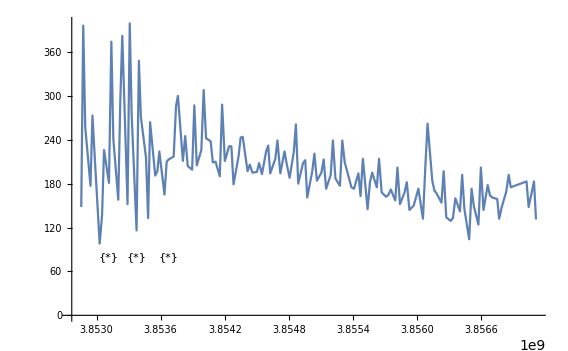

```mathematica
ListLinePlot[gts,Epilog->createEpilog[gs]]
```

Interpolation

```mathematica
Interpolation[gts]
```

InterpolatingFunction[…]

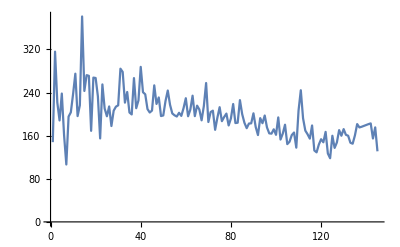

```mathematica
ListLinePlot[Table[Interpolation[gts][t],{t,startTime,endTime,period}]]
```

Fourier(1)

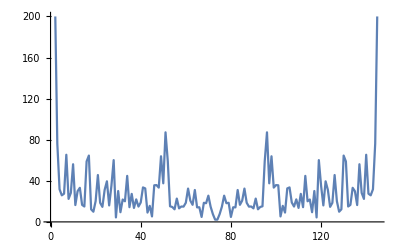

```mathematica
ListLinePlot[Fourier[Table[Interpolation[gts][t],{t,startTime,endTime,period}]]//Abs,PlotRange->{All,{0,200}}]
```

Fourier(2)

InterpolatingFunction::dmval: 入力値{3.85368×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3.85371×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3.85374×10^9}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

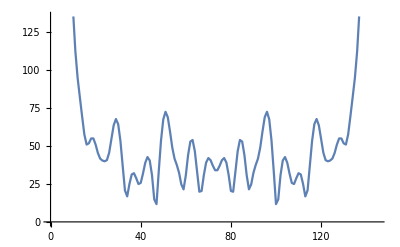

```mathematica
ListPlot[Fourier[InterpolatingFunction[…][Range[startTime,endTime,period]]//N]//Abs,Joined->True]
```

## TimeSeries[]の時刻はなんの時刻か？

UnixTime[]そのものは正しい

```mathematica
Date[]
```

{2022,3,24,16,31,1.52441}

```mathematica
UnixTime[] (* date +%s の値と同じ *)
```

1648107061

```mathematica
UnixTime[Date[]]
```

1648107061

https://keisan.casio.jp/exec/system/1526003938 の値ともおなじ。

```mathematica
Date[UnixTime[]](* これはできないらしい *)
```

Date::zspec: 時刻帯指定1648107061は有効な日付に変換できません．

Date[1648107061]

かわりにDateObjectを使うとおかしくなる。

```mathematica
DateObject[UnixTime[]]
```

Mon 24 Mar 1952 07:31:01GMT+9

```mathematica
DateObject[Date[]]
```

Thu 24 Mar 2022 16:31:01GMT+9

UnixTimeとDateObjectとの関係も正しい？（わかりにくいが）

```mathematica
DateObject[0-UnixTime[0],TimeZone->"Japan"]
```

Thu 1 Jan 1970 09:00:00JST

```mathematica
DateObject[0-UnixTime[0],TimeZone->"UTC"]
```

Thu 1 Jan 1970 09:00:00UTC

つまり、DateObjectに変換したときにシフトが発生するらしい、TimeSeries[]も同じ機能をつかっていると見られ、同等のシフトが発生する。 => UnixTimeとは別にAbsoluteTime[]が導入されていることによる。

```mathematica
DateObject[0]
```

Mon 1 Jan 1900 00:00:00GMT+9

```mathematica
UnixTime[0]
```

-2209021200

```mathematica
gts//Length
```

4

```mathematica
gs[[1]][[1]]//UnixTime
```

1643835900

```mathematica
gs[[-1]][[1]]//UnixTime
```

1648090560

```mathematica
gts[[2]]
```

{{{148,396,257,177,273,204,98,137,226,181,374,241,158,293,382,152,399,275,116,348,271,216,133,264,191,197,224,165,210,213,217,286,300,211,245,204,199,287,205,226,308,242,238,209,210,190,288,211,231,231,179,217,243,244,197,206,195,196,208,193,224,232,194,214,239,194,224,206,188,223,261,180,208,212,161,197,221,184,195,213,173,192,239,187,177,239,209,175,173,194,163,214,145,182,195,175,214,168,162,165,172,157,202,152,168,182,144,150,161,173,132,207,262,184,170,168,154,197,134,129,133,160,142,192,145,104,173,149,124,202,144,178,164,161,159,132,147,169,192,175,183,148,183,131}},{{{3852857100,3852875760,3852894660,3852943560,3852962160,3852988200,3853029420,3853052100,3853070100,3853116480,3853138860,3853157280,3853203420,3853222440,3853241040,3853290180,3853310940,3853328700,3853374720,3853396440,3853415040,3853462860,3853482840,3853501260,3853549500,3853569600,3853587840,3853635780,3853656540,3853674540,3853721820,3853744020,3853761780,3853807920,3853829880,3853853340,3853894680,3853915140,3853938060,3853980900,3854002560,3854024820,3854067660,3854088420,3854113560,3854153460,3854175120,3854200860,3854239980,3854261820,3854282100,3854328720,3854348400,3854367720,3854413200,3854434020,3854459040,3854500560,3854521200,3854547840,3854586960,3854606400,3854625060,3854672940,3854692740,3854719860,3854758740,3854780760,3854806620,3854845440,3854865360,3854887200,3854932020,3854952840,3854971500,3855018660,3855038340,3855061920,3855103980,3855125280,3855148200,3855191340,3855211620,3855235200,3855277380,3855299520,3855322380,3855384900,3855409140,3855449880,3855470280,3855492060,3855536160,3855558240,3855579240,3855622560,3855643200,3855667920,3855709740,3855732480,3855753060,3855794940,3855815400,3855839160,3855882000,3855902820,3855927780,3855967560,3855988680,3856011060,3856054140,3856077720,3856097160,3856141440,3856162320,3856176420,3856227240,3856247940,3856272300,3856313580,3856334640,3856357500,3856400280,3856420920,3856442160,3856486680,3856509180,3856530480,3856572960,3856596120,3856620600,3856660020,3856680660,3856702260,3856749180,3856767060,3856789620,3856833240,3856856400,3856875720,3857023020,3857042940,3857093100,3857111760}}},1,{Continuous,1},{Discrete,1},1,{ResamplingMethod→{Interpolation,InterpolationOrder→1},ValueDimensions→1}}

```mathematica
gts[[2]][[2]][[1]][[1]][[1]]
```

3852857100

2209021200のシフトとは？ -> 1900年 1月 1日を紀元としている

```mathematica
gts[[2]][[2]][[1]][[1]][[1]]-(gs[[1]][[1]]//UnixTime)
```

2209021200

```mathematica
gts[[2]][[2]][[1]][[1]][[-1]]-(gs[[-1]][[1]]//UnixTime)
```

2209021200

```mathematica
DateObject[3852857100]
```

Thu 3 Feb 2022 06:05:00GMT+9

```mathematica
DateObject[0]
```

Mon 1 Jan 1900 00:00:00GMT+9

[不思議ポイントはここか？] 1900 年を紀元とするカレンダーとは？

```mathematica
??CalendarType
```

''' CalendarTypepaclet:ref/CalendarTypeは，デフォルトで，"Gregorian"に設定されている． '''

''' CalendarTypepaclet:ref/CalendarTypeのデフォルト値はAutomaticpaclet:ref/Automaticで，これは，0年がない初期のグレゴリオ暦を使う．西暦以前の年は負で，以後は正である． '''

という説明にもかかわらず、値を負にしても、西暦以前を示さない。。。

```mathematica
DateObject[-1]
```

Sun 31 Dec 1899 23:59:59GMT+9

結論：UnixTimeがあればすべて事足りるはずであるのに、AbsoluteTimeを導入しているために混乱をきたしている。AbsoluteTimeは、なんの役にも立っていないように見える。